# Lab 7: Introduction to NIM

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 5
Partner: Jeremy Watts

## Preamplifier

1. Properly plot the saved input/output traces (one set only) on a single plot.

```mathematica
datadir=NotebookDirectory[]<>"Data/Station5/";
```

```mathematica
inputData=Import[datadir<>"ALL0010.csv"][[17;;,1;;2]];
outputData=Import[datadir<>"ALL0005.csv"][[17;;,1;;2]];
scaleFactor=100;
outputData[[;;,2]]=outputData[[;;,2]]*scaleFactor;
inputData[[;;,1]]=inputData[[;;,1]]*1000; (* scale to ms *)
outputData[[;;,1]]=outputData[[;;,1]]*1000;(* scale to ms *)
```

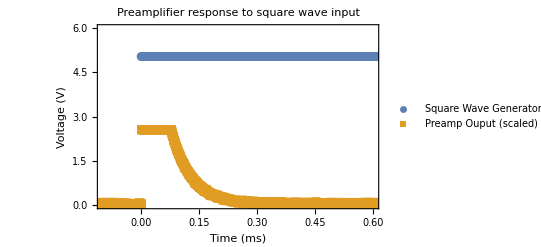

```mathematica
ListPlot[{inputData,outputData}, Axes->True, PlotRange->{{-0.1,0.6},{0, 6}},
Frame->True, ImageSize->Full,
FrameLabel->{Style["Time (ms)",Black,18],Style["Voltage (V)",Black,18]},
PlotLegends->Placed[{"Square Wave Generator", "Preamp Ouput (scaled)"},{0.85, 0.5}],
PlotMarkers->Automatic,
PlotLabel->Style["Preamplifier response to square wave input",Black,30],
FrameTicksStyle->Directive[{Black,18},{Black,18}]]
```

2. From the output decay of the preamplifier, fit an exponential to it and determine the decay time constant. Report the decay time constant in a text-style cell.

The decay occurs from approximately 0.1ms on, so the curve will be fit to data from the time range [0.1,0.4]

```mathematica
fitData=outputData[[13000;;14000,;;]];
fitData[[;;,2]]=fitData[[;;,2]]/scaleFactor;(* transform back for analysis *)
fitData[[;;,2]]=Log[fitData[[;;,2]]];
```

```mathematica
line=Fit[fitData,{1,t},t]
```

-2.66178-15.8308 t

```mathematica
15.830791415674563^-1
```

0.063168

The time constant of this decay is 0.063 ms^-1.

3. The preamplifier board used is the CR-150-R5 from CREMAT. Go to http://www.cremat.com/home/cr-150-r5-csp-evaluation-board/ and find the capacitance of the TEST capacitor.

From the PDF located at http://www.cremat.com/CR-150-R5.pdf, the value of the test capacitor is 1pF=10^-12 F

4. Using Q=CV, calculate the amount of injected charge into the preamplifier for the 5 input/output amplitude sets (i.e., find Q from the input voltage from the function generator).

```mathematica
capacitance=10^-12; (* Farads *)
```

```mathematica
amplitudeArray={1.000, 3.000, 5.000, 7.000, 9.000};
chargeInjected=capacitance*amplitudeArray
```

{1.×10^-12,3.×10^-12,5.×10^-12,7.×10^-12,9.×10^-12}

```mathematica
tableHeadings={"Input Voltage (V)", "Charge injected (pC)"};
dataTable = TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12],2]//First, TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC)
1. | 1.
3. | 3.
5. | 5.
7. | 7.
9. | 9.

The amount of injected charge for the 1.000V input was 1pC, for the 3.000V input was 3pC, for the 5.000V input was 5pC, for the 7.000V input was 7pC, and for the 9.000V input was 9pC.

5. From the injected charge and output voltage, from the preamplifier (saved traces), determine the gain of the preamplifier in units of mV/pC.

```mathematica
maxOutputVoltage[f_]:=Max[Import[datadir<>f][[17;;,2]]]
```

```mathematica
outputFiles={"ALL0001.csv", "ALL0002.csv", "ALL0003.csv", "ALL0004.csv", "ALL0005.csv"};
maxVolts=Table[1000*maxOutputVoltage[f],{f,outputFiles}](* mV *)
outputGain=maxVolts/(chargeInjected*10^12)
```

{13.2,25.6,25.6,25.6,25.6}

{13.2,8.53333,5.12,3.65714,2.84444}

```mathematica
tableHeadings=Append[tableHeadings,"Max Output Voltage (mV)"]
tableHeadings=Append[tableHeadings, "Gain (mV/pC)"]
```

{Input Voltage (V),Charge injected (pC),Max Output Voltage (mV)}

{Input Voltage (V),Charge injected (pC),Max Output Voltage (mV),Gain (mV/pC)}

```mathematica
TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12,maxVolts,outputGain],4]//First,TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC) | Max Output Voltage (mV) | Gain (mV/pC)
1. | 1. | 13.2 | 13.2
3. | 3. | 25.6 | 8.53333
5. | 5. | 25.6 | 5.12
7. | 7. | 25.6 | 3.65714
9. | 9. | 25.6 | 2.84444

6. Report the data (input voltage, injected charge, output voltage, and calculated gain) in a table within the Mathematica notebook as done in a previous laboratory exercise.

```mathematica
TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12,maxVolts,outputGain],4]//First,TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC) | Max Output Voltage (mV) | Gain (mV/pC)
1. | 1. | 13.2 | 13.2
3. | 3. | 25.6 | 8.53333
5. | 5. | 25.6 | 5.12
7. | 7. | 25.6 | 3.65714
9. | 9. | 25.6 | 2.84444

7. The preamplifier used was either a CR-110, CR-111, CR-112, CR-113 (http://www.cremat.com/home/charge-sensitive-preamplifiers/). From the table of data and calculated fall time, determine what preamplifier was used.

Based on the data collected in the lab, the preamplifier appears to be the CR-112, which has a stated fall time of 50μs=0.050ms and a gain of 13mV/pC.

Amplifier Linearity

1. From the data collected, create a properly formatted table of the input voltage to output amplitude from the amplifier.

A lack of understanding of the laboratory procedure occurred: instead of varying the magnitude of the voltage output from the square wave generator, the amplification setting on the amplifier was adjusted, resulting in data that does not match the lab procedure. In order to proceed with the analysis, copies of the data from another station (Station 5, Dory Miller) were used.

```mathematica
datadir=NotebookDirectory[]<>"Data/Station4/Dory/";
```

```mathematica
maxOutputVoltage2[f_,c_]:=Max[Import[datadir<>f][[;;,c]]]
```

```mathematica
inputVoltage={1.00, 2.00, 3.00, 4.00, 5.00, 5.96, 7.04};
```

```mathematica
files=Table["ALL00"<>ToString[i]<>".csv",{i,Range[13,18]}]
```

{ALL0013.csv,ALL0014.csv,ALL0015.csv,ALL0016.csv,ALL0017.csv,ALL0018.csv}

```mathematica
inputVolts=Table[maxOutputVoltage2[f,2],{f,files}]
outputVolts=Table[maxOutputVoltage2[f,4],{f,files}]
```

{0.114,0.17,0.228,0.288,0.352,0.408}

{2.04,3.04,4,4.96,6,6.96}

```mathematica
tableHeaders={"Input Voltage (V)", "Amplifier Output (V)"};
```

```mathematica
TableForm[Multicolumn[Join[inputVolts,outputVolts],2]//First,TableHeadings->{None,tableHeaders}]
```

Input Voltage (V) | Amplifier Output (V)
0.114 | 2.04
0.17 | 3.04
0.228 | 4
0.288 | 4.96
0.352 | 6
0.408 | 6.96

2. Conduct a linear regression on the dataset and report the fitted parameters and their uncertainty (that is, the uncertainty in the y-intercept and slope).

```mathematica
lm=LinearModelFit[Multicolumn[Join[inputVolts,outputVolts],2]//First,x,x]
```

FittedModel[0.18783+16.5853 x]

```mathematica
Normal[lm]
```

0.18783+16.5853 x

```mathematica
lm["RSquared"]
```

0.999751

```mathematica
lm["ParameterErrors"]
```

{0.0364952,0.130787}

A linear model proved to be a very good fit for this data, indicating that the amplifier works well in this range. The intercept was very close to zero at 0.188±0.04V while the slope was 16.6±0.13.

3. Using the “Correlation” command, find the correlation coefficient of the dataset.

```mathematica
Correlation[Multicolumn[Join[inputVolts,outputVolts],2]//First][[1,2]]
```

0.999876

The correlation coefficient for the input and output voltage is 0.999876.

4. In a text-style cell, comment on the linearity (i.e., does the output voltage scale linearly with the input voltage) of the amplifier.

These sets of values are highly correlated, with a correlation coefficient of 0.999876. This matches well with the least-squares fit in part 2.

Amplifier Shaping

1. For the data collected in steps 1-4, correlate the input tail pulse rise to the output amplitude of the amplifier. Data will be reported in step 3.

```mathematica
riseTimes={0.144, 6.40, .630, .300}; (* μs *)
pulseVoltage={5.03, 1.98, 4.01, 4.96}; (* V, ±0.01V *)
Correlation[riseTimes,pulseVoltage]
```

-0.963993

These two values were apparently strongly negatively correlated.

2. For the data collected in step 5, correlate the shaping time of the amplifier to the amplifier output amplitude. Data will be reported in step 3.

```mathematica
shapingTime={ 0.5, 1, 2, 3, 6, 10}; (* μs *)
amplitude={1.92, 2.90, 4.10, 4.80, 5.48, 5.60}; (* V *)
amplitudeErrors={0.01, 0.02, 0.10, 0.50, 0.08, 0.05} ;(*V*)
```

```mathematica
Correlation[shapingTime,amplitude]
```

0.836384

The shaping time and amplitude were less strongly correlated with a value of only 0.836.

3. From these two datasets, provide a properly formatted table that has columns for tail pulse input rise time, shaping time on the preamplifier, and output amplifier amplitude.

```mathematica
riseTimeSetting={10, 5, 1, 0.1, 5, 5, 5, 5, 5, 5};(*μs*)
shapingTimeSetting={0.5, 0.5, 0.5, 0.5, 0.5, 1, 2, 3, 6, 10};(*μs*)
amplitude={5.03, 1.98, 4.01, 4.96, 1.92, 2.90, 4.10, 4.80, 5.48, 5.60};(*V*)
```

```mathematica
TableForm[Multicolumn[Join[riseTimes,shapingTime,amplitude],3]//First]
```

0.144 | 2 | 4.1
6.4 | 3 | 4.8
0.63 | 6 | 5.48
0.3 | 10 | 5.6
0.5 | 1.92 | 
1 | 2.9 |

```mathematica
TableForm[Multicolumn[Join[riseTimeSetting,shapingTimeSetting,amplitude],3]//First,TableHeadings->{None,{"Rise Time (μs)", "Shaping Time (μs)", "Amplitude (V)"}}]
```

Rise Time (μs) | Shaping Time (μs) | Amplitude (V)
10 | 0.5 | 5.03
5 | 0.5 | 1.98
1 | 0.5 | 4.01
0.1 | 0.5 | 4.96
5 | 0.5 | 1.92
5 | 1 | 2.9
5 | 2 | 4.1
5 | 3 | 4.8
5 | 6 | 5.48
5 | 10 | 5.6

4. Upon inspection of the data, discuss/explain the trend in the data below the table, clearly defining the reason behind the trend observed for changes to the rise time from the tail pulse generator and amplifier shaping time. This discussion should appear below the table in a text-style cell within the Mathematica notebook.

For a constant shaping time, the amplitude of the output pulse varies nearly linearly in proportion to the rise time. By contrast the relationship of Amplitude to Shaping time is less linear.